```mathematica
Clear[RealPart];Clear[ImagPart];
For[i=0,i<3,i++,
jj=ToString[i];
inpstr=OpenRead["/home_th/kirscher/compton-scattering-and-the-lit/source/LIT_results/lit-pol-prc/Re_P_J"<>jj];
RealPart[i]=Interpolation[ReadList[inpstr,{Number,Number}]];
  Close[inpstr];
inpstr=OpenRead["/home_th/kirscher/compton-scattering-and-the-lit/source/LIT_results/lit-pol-prc/Im_P_J"<>jj];
ImagPart[i]=Interpolation[ReadList[inpstr,{Number,Number}]];
  Close[inpstr];
]
```

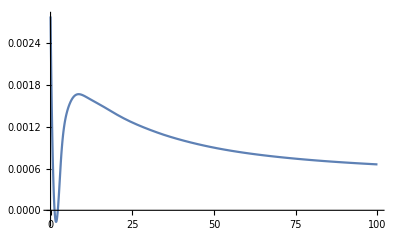

180 °

```mathematica
Plot[ImagPart[0][k],{k,0,100}]
180 Degree
```

```mathematica
amplitude[Mf_,Mi_,λf_,λi_,ω_,θ_]:=
Module[{compo},
ampli=0;
For[j=0,j<3,j++,
compo=(-1)^(λf-Mi)*(RealPart[j][ω]+I ImagPart[j][ω]);
ampli+=(2*j+1) ThreeJSymbol[{1,-Mf},{j,Mf-Mi},{1,Mi}] ThreeJSymbol[{1,λi},{1,Mf-Mi-λi},{j,Mi-Mf}] WignerD[{1,Mf-Mi-λi,-λf},0,θ,0] compo;
];
Return[ampli]
]
```

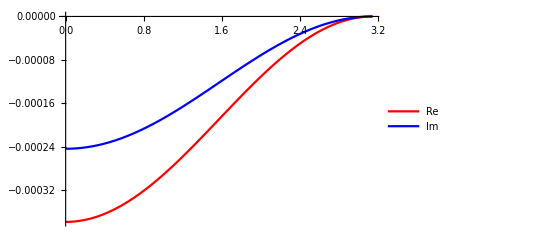

```mathematica
Subscript[ω, 1]=10.974575;
Subscript[ω, 2]=40.974575;
mi=1;mf=1;li=1;lf=1;
Plot[{Re[amplitude[mf,mi,li,lf,Subscript[ω, 2],x]-amplitude[mf,mi,li,lf,Subscript[ω, 1],x]],Im[amplitude[mf,mi,li,lf,Subscript[ω, 2],x]-amplitude[mf,mi,li,lf,Subscript[ω, 1],x]]},{x,0,Pi},PlotLegends->{"Re","Im"},PlotStyle->{Red,Blue}]
```